```mathematica
VertexSetsFromMatrix[mat_]:=Block[{
result = {}, (* Will contain the vertext sets, a set of sets.  These are order so that 1 comes before 2 etc.*)
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col (* current column in the matrix *)
},
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
todo = Select[todo,#≠col&];
]
]
];
result = Append[result,bucket]
]
];
result
]
```

```mathematica
GraphFromMatrix[mat_,vertexSets_]:=Block[{
edges={},
vertices={},
vertexLabels={},
bucket = {}, (* Contains the current set of vertices that will go into result later *)
todo=Range[Length[mat]], (* contains vertices that have not yet been put in a bucket *)
row, (* current row in the matrix, also current vertex number *)
col, (* current column in the matrix *)
vertexToVertex=Association[],
newVertexToVertex=Association[],
currentVertex=0,
countNodes=Length[mat],
myvertexSets=vertexSets
},
If[myvertexSets==Null,myvertexSets=VertexSetsFromMatrix[mat]];
For[row=1, row≤Length[mat], row++,
(* only process row if it has not yet been put in a bucket *)
If[MemberQ[todo,row],
currentVertex++;
(* now collect all columns that are marked with '2' and put them in the bucket *)
bucket={};
For[col=1, col ≤ Length[mat], col++,
If[MemberQ[todo,col],
If[mat[[row,col]]==2,
bucket = Append[bucket,col];
vertexToVertex[col]=currentVertex;
todo = Select[todo,#≠col&]
]
]
];
newVertexToVertex[currentVertex]=bucket
]
];

(* now compute the edges *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
If[mat[[row,col]]==1,
edges=Append[edges,Sort[{vertexToVertex[row],vertexToVertex[col]}]]
]
]
];
edges=DeleteDuplicates[edges];
Graph[
Keys[newVertexToVertex],
edges,
VertexLabels->Table[i->StringRiffle[ newVertexToVertex[i],","],{i,Length[Keys[newVertexToVertex]]}],
VertexStyle->Red,
VertexSize->0.1,
VertexCoordinates->MyCircle[myvertexSets,countNodes],
EdgeStyle->{Thickness[0.02],Darker[Darker[Green]]},
ImageSize->{50,50}
]
]
```

```mathematica
allGraphs=Association[];
```

```mathematica
ComputeComp[assoc_,key_]:=Block[{current,g, clique},
current = assoc[key];
g=current["graph"];
current["comp"]=GreaterEqual;
current["compwhy"] = "No IH";
If[MyPlanar[assoc,key],
current["comp"]=Greater;
current["compwhy"] = "This is a planar contraction"
,
(* not planar contraction - look for K5 *)
clique=First[FindClique[g]];
If[Length[clique]≥5,
current["comp"]=Equal;
current["compwhy"] = "This graph contains Clique of size"<> ToString[Length[clique]]
]
];
current
]
```

## Compute color table

the following procedure only works if the vertexset represents a complete graph.

```mathematica
ComputeColorTable[vertexSets_]:=Block[
{vertexCount=Length[Flatten[vertexSets]], combinations, vertexToBucketNumber=Association[],left,right,colofour},

Table[Table[vertexToBucketNumber[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
combinations=Subsets[Range[vertexCount],{2}];
colofour=PartitionToSymbol[vertexSets];
Table[
left=vertexToBucketNumber[c[[1]]];
right=vertexToBucketNumber[c[[2]]];

If[left==right,
{colofour,0},
{0,colofour}
]
,{c,combinations}
]
]
```

```mathematica
globalDepth=1
```

1

```mathematica
ComputeGraph[mat_,depth_]:=Block[{result,row,col,g, matJoin,matContract, rowBucket, colBucket,i,j, vertexSets,current,key,leftKey,rightKey, left, right,vertexSetLength,compressed, fromVertexToVertexSet,size,max,max2},
If[depth≤0,Interrupt[]];
(* first see if we can find it *)
globalDepth=depth;
key=GraphMatrixSignature[mat];

If[KeyExistsQ[allGraphs,key],
current = allGraphs[key];
result=key;
Return[key]
,
(* cannot find it : create an entry *)
vertexSets = VertexSetsFromMatrix[mat];
g=GraphFromMatrix[mat,vertexSets];
current=Association[];
current["signature"]=GraphMatrixSignature[mat];
current["matrix"]=mat;
current["graph"]=g;
current["vertexsets"]=vertexSets;
current["vertices"]=VertexList[g];
current["edges"]=EdgeList[g];
current["relations"]={};
current["links"]={};
current["parents"]={};
current["children"]={};
allGraphs[key]=current;
current=ComputeComp[allGraphs,key];
];

(*If[ToString[current["comp"]]=="Equal",
(* no need to go deeper iw we already have K5 *)
result=key;
current["colofour"]=0;
allGraphs[key]=current;
Return[key]
];*)
g=current["graph"];
vertexSets = current["vertexsets"];
vertexSetLength=Length[vertexSets];
size=Length[Flatten[vertexSets]];

(* see if it is a complete graph *)
If[CompleteGraphQ[g],
(* complete graph - try set comp and compwhy, colofour and colortable*)
result=key;
current["colofour"]=PartitionToSymbol[vertexSets];
current["colortable"]=ComputeColorTable[vertexSets];
,
(*  not a complete graph *)
For[row=1, row≤Length[mat], row++,
For[col=row+1, col ≤ Length[mat], col++,
(*for every vertex couple thatis not connected we compute the connected and the contracted form *)
If[mat[[row,col]]==0,
matJoin=mat;
matContract=mat;

(* first compute to which vertex set row and column belong*)
fromVertexToVertexSet=Association[];
Table[Table[fromVertexToVertexSet[v]=k,{v,vertexSets[[k]]}],{k,Length[vertexSets]}];
rowBucket=vertexSets[[fromVertexToVertexSet[row]]];
colBucket=vertexSets[[fromVertexToVertexSet[col]]];

(* now set the entries in contract and joined *)
Table[
matContract[[r,c]]=2;
matContract[[c,r]]=2;
matJoin[[r,c]]=1;
matJoin[[c,r]]=1
,
{r,rowBucket},
{c,colBucket}
];
(* now make sure the entries are consistent.  We take the max of the other entries *)
Table[
max=Max[Table[matContract[[r,v]],{r, rowBucket}]];
max2=Max[Table[matContract[[r,v]],{r, colBucket}]];
max=Max[max,max2];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, rowBucket}];
Table[matContract[[r,v]]=max;matContract[[v,r]]=max,{r, colBucket}];
,
{v,size}
];

(* compute left and right *)
leftKey=ComputeGraph[matJoin,depth-1];
rightKey = ComputeGraph[matContract,depth-1];
left=allGraphs[leftKey];
right=allGraphs[rightKey];

(* if my position is not clear yet, try to see if the children can help *)
If[ToString[current["comp"]]=="GreaterEqual",
If[ToString[left["comp"]]=="Greater"||ToString[right["comp"]]=="Greater",
current["comp"]=Greater;
current["compwhy"]="The relation holds x"<> ToString[key]<> "== x"<> ToString[leftKey]<>"("<>ToString[left["comp"]]<> ") + "<> ToString[rightKey]<> 
" (" <>ToString[right["comp"]]<>")"
]
];

current["colofour"]=left["colofour"]+right["colofour"];
current["colortable"]=left["colortable"]+right["colortable"];
current["relations"]=Append[current["relations"],Symbol["x"<>ToString[key]]==Symbol["x"<>ToString[leftKey]]+Symbol["x"<>ToString[rightKey]]];
left["relations"]=Append[left["relations"],Symbol["x"<>ToString[leftKey]]==Symbol["x"<>ToString[key]]-Symbol["x"<>ToString[rightKey]]];
right["relations"]=Append[right["relations"],Symbol["x"<>ToString[rightKey]]==Symbol["x"<>ToString[key]]-Symbol["x"<>ToString[leftKey]]];

current["children"]=Append[current["children"],{leftKey,rightKey}];
left["parents"]=Append[left["parents"],key];
right["parents"]=Append[right["parents"],key];

allGraphs[leftKey]=left;
allGraphs[rightKey]=right;
result=key;

(* force a premature stop *)
col=size+1;
row=col;
]
]
]
];
allGraphs[key]=current;
result
]
```

```mathematica
DependencyGraph[assoc_,startKey_]:=Block[{todo={startKey},edges={}, children,currentKey, vertexColors={},vertices={},vertexLabels={},g,mat,size,visited={}},
If[ListQ[startKey],
todo=startKey;
edges=Table["root"->k,{k,startKey}];
vertices={"root"}
];
Monitor[
While[todo≠{},
currentKey=First[todo];
todo=Rest[todo];
vertices=Append[vertices,currentKey];
vertexColors=Append[vertexColors,currentKey->ColourForKey[assoc,currentKey]];
mat=assoc[currentKey]["matrix"];
size=Length[mat];
vertexLabels=Append[vertexLabels,currentKey->
Tooltip[
currentKey,
Labeled[
Column[
{
MatrixForm[mat,TableHeadings->{Table[Style[k,Red],{k,size}],Table[Style[k,Red],{k,size}]}]
,
Row[{
assoc[currentKey]["graph"],
Graph[
VertexList[assoc[currentKey]["graph"]],
EdgeList[assoc[currentKey]["graph"]],
VertexLabels->PropertyValue[assoc[currentKey]["graph"],VertexLabels],
ImageSize->{80,80}]
}],
Style[assoc[currentKey]["colofour"],Italic]
}
],Style[assoc[currentKey]["compwhy"],Bold]]]];
children=assoc[currentKey,"children"];
Table[
Table[
If[!MemberQ[visited,child],
edges=Append[edges,currentKey->child];
If[!MemberQ[todo,child],
todo=Append[todo,child]
];
],
{child,childCouple}
]
,
{childCouple,children}
]
],
visited
];
Graph[vertices,DeleteDuplicates[edges],VertexStyle->vertexColors, VertexLabels->vertexLabels,GraphLayout->"RadialEmbedding"]
]
```

## Now for the exercises

```mathematica
1
```

```mathematica
Length[allGraphs]
```

9

```mathematica
allGraphs=Association[];
```

```mathematica
ComputeGraph[
{
{2,1,0,1},
{1,2,1,0},
{0,1,2,1},
{1,0,1,2}}
,10]
```

280

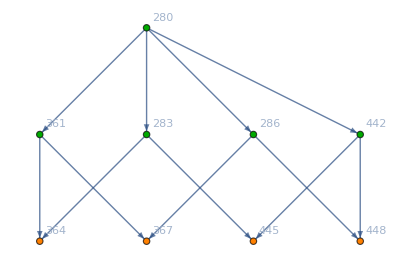

```mathematica
DependencyGraph[allGraphs,280]
```

```mathematica
allGraphs=Association[];ComputeGraph[
{
{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{1,1,1,1,1,2}}
,10]
```

5039860

```mathematica
Keys[allGraphs]//Length
```

57

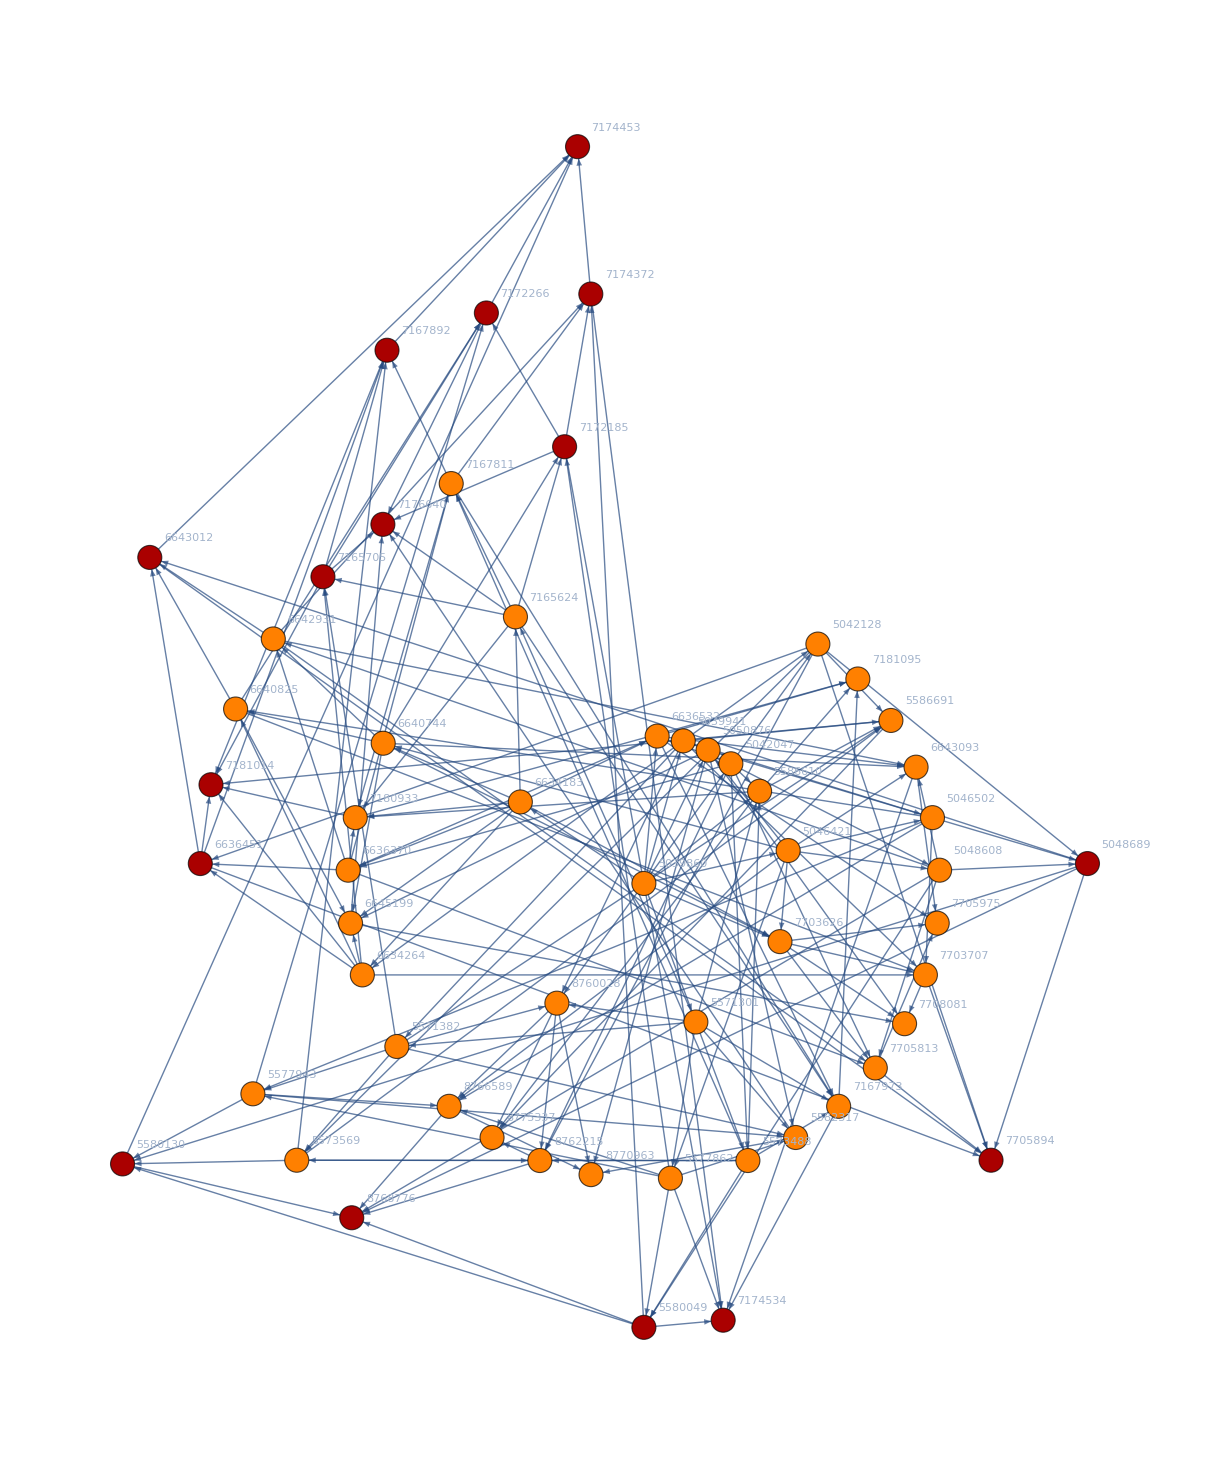

```mathematica
DependencyGraph[allGraphs,5039860]
```

```mathematica
ComputeGraph[
withColorTables5[lambdaKey,"matrix"]
,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
GraphFromMatrix[
{{2,1,0,0,1,1},
{1,2,1,0,0,1},
{0,1,2,1,0,1},
{0,0,1,2,1,1},
{1,0,0,1,2,1},
{1,1,1,1,1,2}}]
```

-Graphics-